```mathematica
dir=NotebookDirectory[];
fileName="PFK var F6P w 2mM AMP.xlsx"
file=FileNameJoin[{dir,fileName}]
```

PFK var F6P w 2mM AMP.xlsx

C:\Users\User\OneDrive - Stellenbosch University\Documents\PhD Folder\Enzymatic Work\Enzyme Characterisation\Phosphofructokinase\08062023\PFK var F6P w 2mM AMP.xlsx

```mathematica
fileData=Import[file,"Data"][[1]];
```

```mathematica
repeats=1
conc=Table[{0,0.1,0.25,0.5,1,2.5,5,10},{i,1,repeats}]
```

1

{{0,0.1,0.25,0.5,1,2.5,5,10}}

```mathematica
proteinDilution=1;
proteinConc=3.148/proteinDilution; (*mg·mL^-1 from bradford*)
lysateDilutionInWell=100/20; (*20μL in 100μL assay*)
pathLength=0.26; (*10μL well volume*)
NADHExt=6.22 (*mM^-cm^-1*);
```

```mathematica
absorbance=fileData[[13;;,3;;]];
time=fileData[[12,3;;]]/60;
data=Table[Thread[{time,absorbance[[i]]}],{i,1,Length[absorbance]}];
```

```mathematica
dataPlots=Table[ListPlot[data[[i]],Axes->False,Frame->True,FrameLabel->{"time (min)","Abs"},PlotRange->{0,1.5},PlotLabel->ToString[Flatten[conc][[i]]]<>" mM",ImageSize->400],{i,1,Length[data]}];
```

```mathematica
Table[range[i],{i,Length[dataPlots]}];
```

```mathematica
rangeCheck[r_]:=Module[{},
Manipulate[range[r]={Ceiling[p[[1]]],Ceiling[q[[1]]]};Show[dataPlots[[r]],Epilog->{Gray,Opacity[0.2],Rectangle[{p[[1]],-1},{q[[1]],2}]}],
{{p,{0,0}},Locator,Appearance->None},{{q,{data[[1,-1,1]],0}},Locator,Appearance->None}]]
```

```mathematica
Table[rangeCheck[i],{i,Length[dataPlots]}]
```

{,,,,,,,}

```mathematica
positionNearest[x_]:=#&@@FirstPosition[time,Nearest[time,x][[1]]]
```

```mathematica
ranges=Table[range[i],{i,1,Length[dataPlots]}];
(*Export[FileNameJoin[{dir,"rangesF6PwAMP.mx"}],ranges]*)
(*Import[FileNameJoin[{dir,"rangesATP.mx"}]]*)
fits=Table[LinearModelFit[data[[i,positionNearest[ranges[[i,1]]];;positionNearest[ranges[[i,2]]]]],x,x],{i,1,Length[data]}]
rates=-Table[D[fits[[i]][x],x],{i,1,Length[fits]}]*(proteinDilution/(NADHExt*pathLength*proteinConc))
```

{FittedModel[1.20809-0.00153516 x],FittedModel[1.21936-0.00521584 x],FittedModel[1.22477-0.009351 x],FittedModel[1.22217-0.0142889 x],FittedModel[1.30699-0.0258173 x],FittedModel[1.56126-0.0607591 x],FittedModel[1.72855-0.0840954 x],FittedModel[1.52975-0.0816964 x]}

{0.000301548,0.00102453,0.00183679,0.00280672,0.00507122,0.0119347,0.0165186,0.0160474}

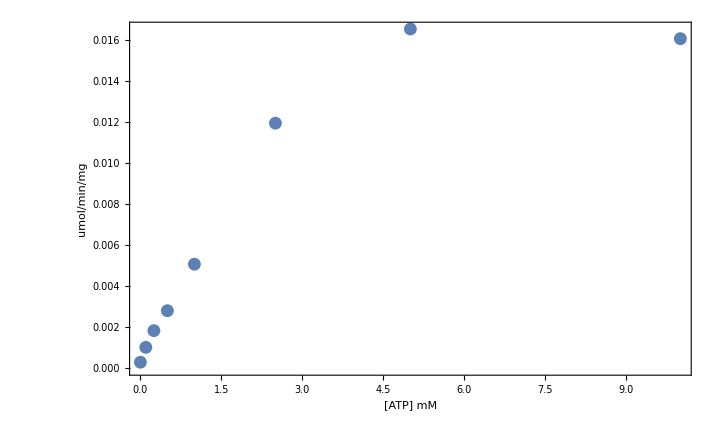

```mathematica
ListPlot[Thread[{Flatten[conc],rates}],Axes->False,Frame->True,FrameLabel->{"[ATP] mM","umol/min/mg"},LabelStyle->Directive[Black,FontSize->16],PlotRange->All]
```

```mathematica
rateData=Drop[Thread[{Flatten[conc],rates}]];
headings={{"F6P mM", "V (umol/min/mg)"}};
```

```mathematica
dataForExport=Join[headings,SortBy[rateData,First]];
MatrixForm[dataForExport]
```

(F6P mM | V (umol/min/mg)
0 | 0.000301548
0.1 | 0.00102453
0.25 | 0.00183679
0.5 | 0.00280672
1 | 0.00507122
2.5 | 0.0119347
5 | 0.0165186
10 | 0.0160474)

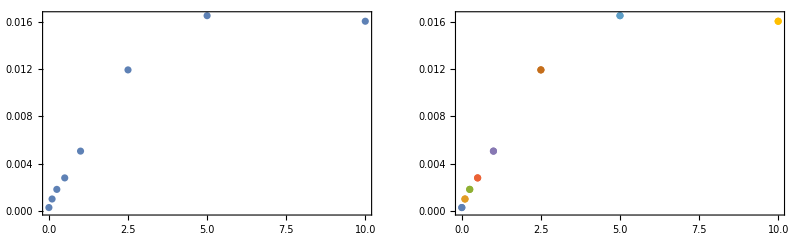

```mathematica
GraphicsRow[{ListPlot[Thread[{DeleteDuplicates@conc[[1]],MeanAround[#[[;;,2]]]&/@GatherBy[rateData,First]}],Axes->False,Frame->True,PlotRange->Full],
ListPlot[GatherBy[rateData,First],Axes->False,Frame->True,PlotRange->All]},ImageSize->Full]
```

```mathematica
(*Export[FileNameJoin[{dir,"data1.csv"}],dataForExport]*)
```

### Data formatting:

```mathematica
allDataHeadings={{"F6P","ATP","ADP","F16BP","AMP","V(umol/min/mg)"}}
```

{{F6P,ATP,ADP,F16BP,AMP,V(umol/min/mg)}}

#### vary F6P

```mathematica
(*dataFormatted={#[[1]],2,0,0,2,#[[2]]}&/@SortBy[rateData,First]*)
```

#### vary ATP:

```mathematica
(*dataFormatted={1,#[[1]],0,0,0,#[[2]]}&/@SortBy[rateData,First]*)
```

#### vary ADP:

```mathematica
(*dataFormatted={10,2,#[[1]],0,0,#[[2]]}&/@rateData*)
```

#### vary F16BP:

```mathematica
(*dataFormatted={2.5,5,#[[1]],0,0,#[[2]]}&/@rateData*)
```

#### vary AMP:

```mathematica
(*dataFormatted={2.5,5,0,#[[1]],#[[2]]}&/@rateData*)
```

#### For Exporting

```mathematica
(*Export[FileNameJoin[{dir,"dataVarF6PwAMP.csv"}],Join[allDataHeadings,dataFormatted]];*)
```